# Test for inherent g

```mathematica
plist={3.70,3.71,3.72,3.73,3.74,3.75,3.76,3.77}
```

{3.7,3.71,3.72,3.73,3.74,3.75,3.76,3.77}

```mathematica
ka1=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgAffineG_N1024_p3.7"<>ToString[p]<>"0_KA1.000000.4.nc","Data"],{p,0,7}];
ka001=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgAffineG_N1024_p3.7"<>ToString[p]<>"0_KA0.010000.4.nc","Data"],{p,0,7}];
```

```mathematica
ka12=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgRightAffineOldPaper_Bi_N1024_p3.7"<>ToString[p]<>"0_KA1.000000.4.nc","Data"],{p,0,7}];
ka0012=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N1024/inherentgRightAffineOldPaper_Bi_N1024_p3.7"<>ToString[p]<>"0_KA0.010000.4.nc","Data"],{p,0,7}];
```

```mathematica
Mean[Normal[ka1[[1,1]]]]
```

0.290506

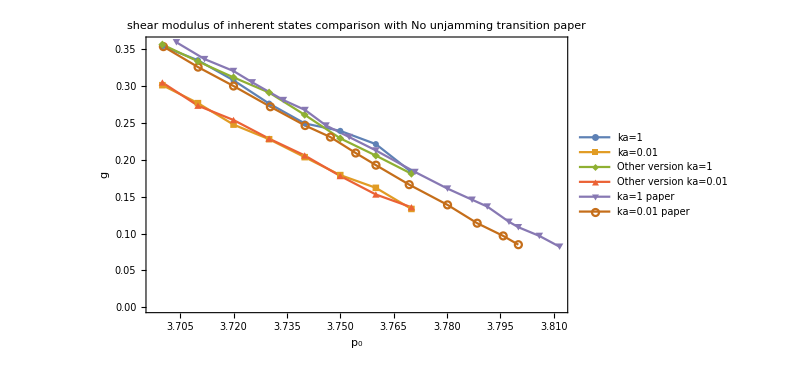

```mathematica
comparisonPlot=ListPlot[{Table[{plist[[p]],Mean[Normal[ka1[[p,1]]]]},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka001[[p,1]]]]},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka12[[p,1]]]]},{p,Length[plist]}],Table[{plist[[p]],Mean[Normal[ka0012[[p,1]]]]},{p,Length[plist]}],ka1paper,ka001paper},PlotLegends->{"ka=1","ka=0.01","Other version ka=1","Other version ka=0.01","ka=1 paper","ka=0.01 paper"},PlotMarkers->Automatic,PlotLabel->"shear modulus of inherent states
comparison with No unjamming transition paper",ImageSize->600,PlotRange->All,Joined->True,FrameLabel->{"p_0","g"}]
```

```mathematica
_Bi
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG.jpeg",comparisonPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG.jpeg

```mathematica
ka001paper={{3.700290275761974,0.35321790036645884},
{3.7100435413642963,0.3254284487528356},
{3.72,0.2998253348649752},
{3.7303628447024675,0.2717463384608707},
{3.7401161103047897,0.2462969732032361},
{3.7472278664731498,0.2306690483206846},
{3.7543396226415098,0.2090666197558951},
{3.7600290275761976,0.19261828373526146},
{3.769375907111756,0.16620365470595697},
{3.780145137880987,0.13878698920837695},{3.7884760522496372,0.11400909592048815},
{3.795791001451379,0.09677543331340013},
{3.8000580551523946,0.08488395818952281}};
```

```mathematica
ka1paper={{3.703947750362845,0.35905430842063735},{3.711872278664732,0.33627175576570095},
{3.72,0.3201386271998944},
{3.7252830188679247,0.30477950903745404},
{3.7340203193033386,0.2808009524285364},
{3.7401161103047897,0.26732911666101833},
{3.7460087082728593,0.2462969732032361},
{3.7525108853410742,0.2306690483206846},
{3.7600290275761976,0.21252113919598364},
{3.77100145137881,0.18337714027808946},
{3.780145137880987,0.16084430702439717},
{3.787053701015965,0.14578104787522406},
{3.791320754716981,0.13653101432481698},
{3.7974165457184323,0.11589292911520903},
{3.8000580551523946,0.1085393430476416},
{3.8059506531204645,0.09677543331340013},
{3.8116400580551524,0.08214681835147608},};
```

### dynamical matrix

```mathematica
eigenValue=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_N512_p3.800_KA1.000000.4.nc","Data"][[1]]
```

NumericArray[…]

```mathematica
eigenValue150=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_N512_p3.800_KA1.0000_alpha1.50.nc","Data"][[1]]
```

NumericArray[…]

```mathematica
eigenValue120=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_N512_p3.800_KA1.0000_alpha1.20.nc","Data"][[1]]
```

```mathematica
eigenValue090=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_N512_p3.800_KA1.0000_alpha0.90.nc","Data"][[1]]
```

NumericArray[…]

```mathematica
Position[Normal[Sort[Normal[eigenValue120]]],_?(#<0&)]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91}}

```mathematica
omega34=Sort[Sqrt[Normal[eigenValue34]]][[97;;]];
```

```mathematica
omega120=Sort[Sqrt[Normal[eigenValue120]]][[100;;]];
```

```mathematica
omega090=Sort[Sqrt[Normal[eigenValue090]]][[100;;]];
```

```mathematica
omegaPaper={{0.07049363493661917,0.011844845812380074},
{0.07149657908375064,0.014844604367798338},
{0.07349461758435658,0.02889244623100332},
{0.07557325385392874,0.05080218046913025},
{0.07828433906916489,0.0913659372639179},
{0.08172105522694333,0.15013107289081742},
{0.0860291820648418,0.18188794722680995},
{0.08795808689936975,0.1881524179950017},
{0.09343150803114131,0.14030037231905743},
{0.09562034022767164,0.10700689556931757},
{0.10311322210531967,0.0745674032861936},
{0.10705365957647454,0.06660846290809168},
{0.1126849477496397,0.08347734492114166},
{0.11684217171458508,0.11069236005176092},
{0.12026059262771978,0.1451325098771507},
{0.12110866185069102,0.16431842915062747},
{0.12672955951703085,0.12818675015407316},
{0.13362432226227208,0.09451270565580325},
{0.1388014664156565,0.07208470695348568},
{0.1398719244672376,0.06660846290809168},
{0.1539113738229757,0.08832393945545251},
{0.15606704068744018,0.11844845812380062},
{0.16543502102821392,0.16806999845478415},
{0.17286125419878762,0.2059327837370163},
{0.19167890514085395,0.2523252918877476},
{0.2112258155304943,0.2130253917058346},
{0.20199690653598712,0.2203622788364574},
{0.2256972405130118,0.2551894671627049},
{0.25020283144058486,0.3383855153428237},
{0.2815613604923351,0.4288969335171299},
{0.32161561652226406,0.5314840014580978},
{0.356652616355998,0.6366805292623694},
{0.4485905235290507,0.8442490648167114},
{0.5520758311802757,0.9558553094685296},
{0.6311181782395525,0.9240304320176029},
{0.7111751893877176,0.771356070911649},
{0.8019127797928729,0.5255187735318169},
{0.8646568168787315,0.37881866788596175},
{0.9252761060043514,0.28568165487569974},
{1.107044517262847,0.2036214517136351},
{1.374035971517909,0.16618362775387507},
{1.5943853506758143,0.15706464294715555},
{1.8225255452914317,0.15530179328137206},
{2.038143046639197,0.13716866187107093},
 {2.2439440168950653,0.15355872934766562},
{2.526838483914687,0.15884750293528313},
{2.802317855865288,0.1860406478285584},
{3.01663283681529,0.2228636380377278},
{3.153653987834591,0.23315624847200317},
{3.373767241500399,0.1924481433101814},
{3.478800109044823,0.1435035831388947},
{3.6968924149541014,0.09345192145605383},
{ 3.755501430036201,0.07127564834438918},
{3.8469822024245275,0.040996341111711965},
{3.9722394533262717,0.019907632173838747},
{3.9799122594329024,0.010944997993195454}
};
```

```mathematica
omegaPaper={{0.07049363493661917,0.011844845812380074},
{0.07149657908375064,0.014844604367798338},
{0.07349461758435658,0.02889244623100332},
{0.07557325385392874,0.05080218046913025},
{0.07828433906916489,0.0913659372639179},
{0.08172105522694333,0.15013107289081742},
{0.0860291820648418,0.18188794722680995},
{0.08795808689936975,0.1881524179950017},
{0.09343150803114131,0.14030037231905743},
{0.09562034022767164,0.10700689556931757},
{0.10311322210531967,0.0745674032861936},
{0.10705365957647454,0.06660846290809168},
{0.1126849477496397,0.08347734492114166},
{0.11684217171458508,0.11069236005176092},
{0.12026059262771978,0.1451325098771507},
{0.12110866185069102,0.16431842915062747},
{0.12672955951703085,0.12818675015407316},
{0.13362432226227208,0.09451270565580325},
{0.1388014664156565,0.07208470695348568},
{0.1398719244672376,0.06660846290809168},
{0.1539113738229757,0.08832393945545251},
{0.15606704068744018,0.11844845812380062},
{0.16543502102821392,0.16806999845478415},
{0.17286125419878762,0.2059327837370163},
{0.19167890514085395,0.2523252918877476},
{0.2112258155304943,0.2130253917058346},
{0.20199690653598712,0.2203622788364574},
{0.2256972405130118,0.2551894671627049},
{0.25020283144058486,0.3383855153428237},
{0.2815613604923351,0.4288969335171299},
{0.32161561652226406,0.5314840014580978},
{0.356652616355998,0.6366805292623694},
{0.4485905235290507,0.8442490648167114},
{0.5520758311802757,0.9558553094685296},
{0.6311181782395525,0.9240304320176029},
{0.7111751893877176,0.771356070911649},
{0.8019127797928729,0.5255187735318169},
{0.8646568168787315,0.37881866788596175},
{0.9252761060043514,0.28568165487569974},
{1.107044517262847,0.2036214517136351},
{1.374035971517909,0.16618362775387507},
{1.5943853506758143,0.15706464294715555},
{1.8225255452914317,0.15530179328137206},
{2.038143046639197,0.13716866187107093},
 {2.2439440168950653,0.15355872934766562},
{2.307786403453253,0.1535064733117435},
{2.4891586491055206,0.15704344694013841},
{2.624565215623139,0.16067100595577394},
{2.7466976725595678,0.17211290673148266},
{2.8314742218190245,0.18866040679995222},
{2.9409675580791728,0.20443365505730204},
{3.0548102199705403,0.22667260818065324},
{3.1726408240883814,0.23191728326267314},
{3.294581488358627,0.2189548718191751},
{3.3697299860733336,0.20203074650966507},
{3.4463976243518926,0.18010169165266132},
{3.5248095943079165,0.160552885620301},
{3.577847971925231,0.1431286677045815},
{3.6314789797835454,0.12327431831513576},
{3.68591390246062,0.1061741005472587},
{3.7414469959144805,0.09574467173095912},
{3.768993424752618,0.08341733208641529},
{3.767998527275057,0.0710282550219008}
};
```

```mathematica
binWidth=150;
Dos=Table[{(omega[[(i+1)*binWidth]]+omega[[i*binWidth]])/2,binWidth/(omega[[(i+1)*binWidth]]-omega[[i*binWidth]])/Length[omega]},{i,Floor[Length[omega]/binWidth]-2}];
```

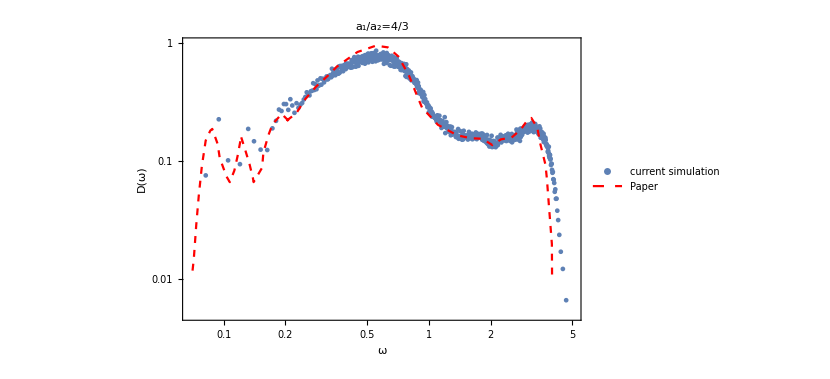

```mathematica
Show[ListLogLogPlot[Dos,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"},PlotLabel->"a_1/a_2=4/3",PlotRange->{All,{0.005,1}}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}]]
```

```mathematica
binWidth=200;
Dos34=Table[{(omega34[[(i+1)*binWidth]]+omega34[[i*binWidth]])/2,binWidth/(omega34[[(i+1)*binWidth]]-omega34[[i*binWidth]])/Length[omega34]},{i,Floor[Length[omega34]/binWidth]-2}];
```

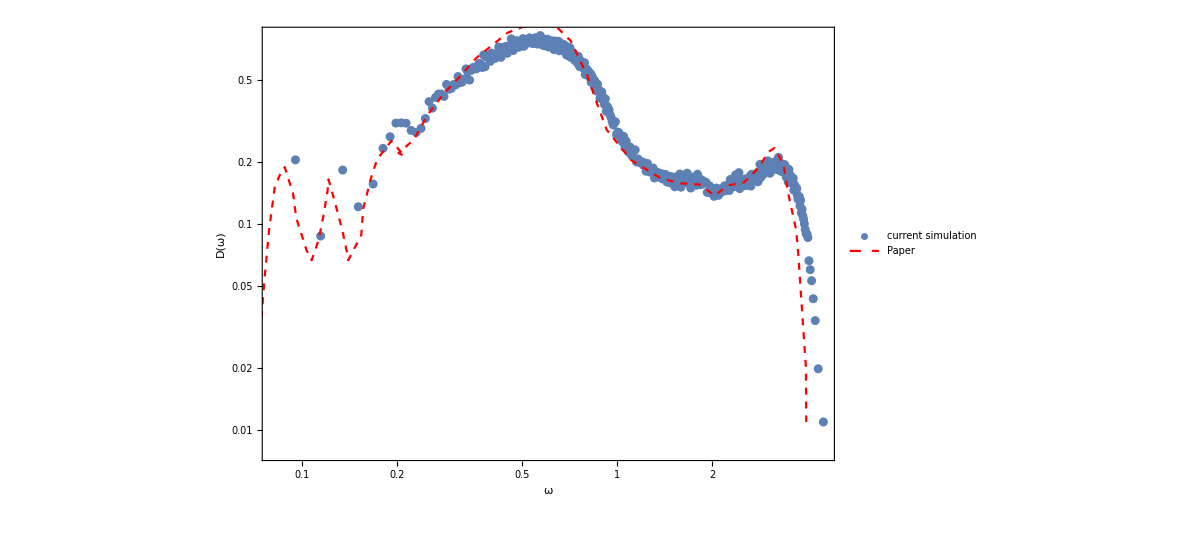

```mathematica
Show[ListLogLogPlot[Dos34,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}]]
```

```mathematica
binWidth=200;
Dos120=Table[{(omega120[[(i+1)*binWidth]]+omega120[[i*binWidth]])/2,binWidth/(omega120[[(i+1)*binWidth]]-omega120[[i*binWidth]])/Length[omega120]},{i,Floor[Length[omega120]/binWidth]-2}];
```

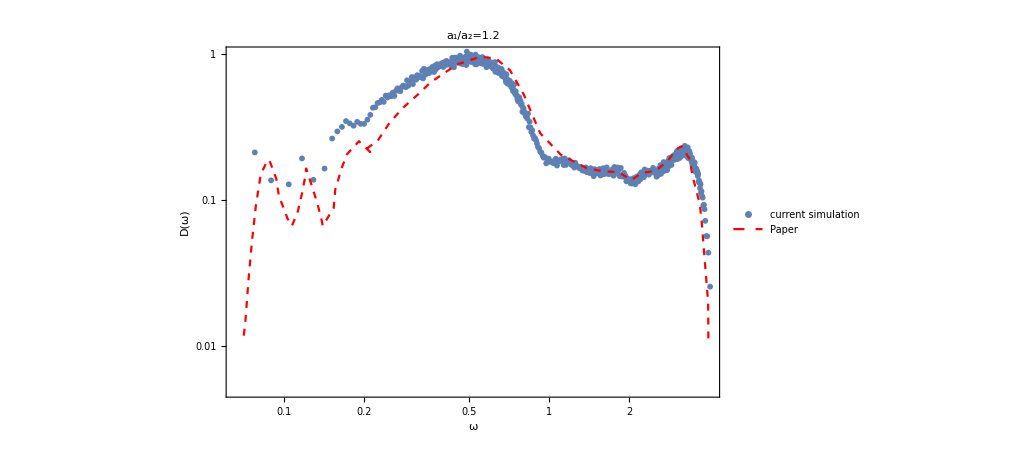

```mathematica
Show[ListLogLogPlot[Dos120,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"},PlotRange->{All,{0.005,1}}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}],PlotLabel->"a_1/a_2=1.2"]
```

```mathematica
binWidth=200;
Dos090=Table[{(omega090[[(i+1)*binWidth]]+omega090[[i*binWidth]])/2,binWidth/(omega090[[(i+1)*binWidth]]-omega090[[i*binWidth]])/Length[omega090]},{i,Floor[Length[omega090]/binWidth]-2}];
```

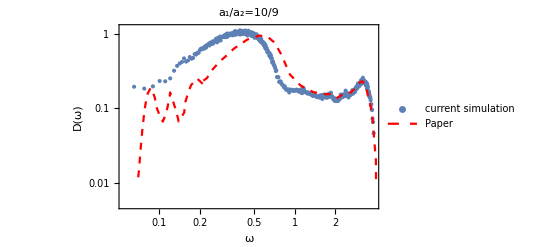

```mathematica
Show[ListLogLogPlot[Dos090,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"},PlotRange->{All,{0.005,1.2}}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}],PlotLabel->"a_1/a_2=10/9"]
```

## Test with T=0.02

```mathematica
Mean[Normal[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/inherentgAffineG_N512_p3.800_KA1.0000_T0.02.nc","Data"][[1]]]]
```

0.0122986

```mathematica
eigenValueT02=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_N512_p3.800_KA1.0000_T0.02.nc","Data"][[1]]

Position[Normal[Sort[Normal[eigenValueT02]]],_?(#<10^(-12)&)]

omega=Sort[Sqrt[Normal[eigenValueT02]]][[50;;]];
```

NumericArray[…]

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40}}

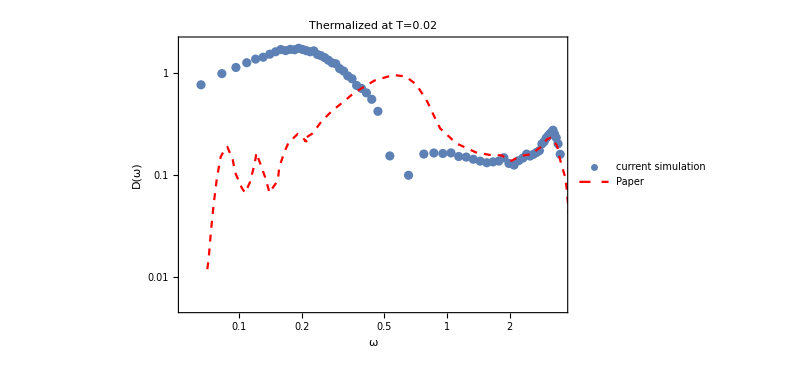

```mathematica
binWidth=300;
Dos=Table[{(omega[[(i+1)*binWidth]]+omega[[i*binWidth]])/2,binWidth/(omega[[(i+1)*binWidth]]-omega[[i*binWidth]])/Length[omega]},{i,Floor[Length[omega]/binWidth]-2}];
plotT02=Show[ListLogLogPlot[Dos,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"},PlotRange->{All,{0.005,2}}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}],PlotLabel->"Thermalized at T=0.02",ImageSize->600]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/ThermalizedDomega.jpeg",plotT02,ImageResolution->600]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/ThermalizedDomega.jpeg

## Test with alpha=1.0301

```mathematica
tsetdata=Import["/home/chengling/Research/Project/Cell/glassAging/fluidConfigurations/monodisperseFluidConfigurations_N512_TEq0.02000000_p3.80000.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/postion→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
g=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/inherentgAffineG_Bi_NoNormalization_N512_p3.760_KA1.0000_alpha1.0302.nc","Data"][[1]]
```

NumericArray[…]

```mathematica
Mean[Normal[g]]
```

0.21149

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_NoNormalization_N512_p3.800_KA1.0000_alpha1.0301.nc","Data"][[1]]
```

Import::format: Cannot import data as Data.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

$Failed⟦1⟧

```mathematica
eigenValue=Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/eigenValue_Bi_NoNormalization_N512_p3.800_KA1.0000_alpha1.0301.nc","Data"][[1]]

Position[Normal[Sort[Normal[eigenValue]]],_?(#<10^(-12)&)]

omega=Sort[Sqrt[Normal[eigenValue]]][[201;;]];
```

NumericArray[…]

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196},{197},{198},{199},{200}}

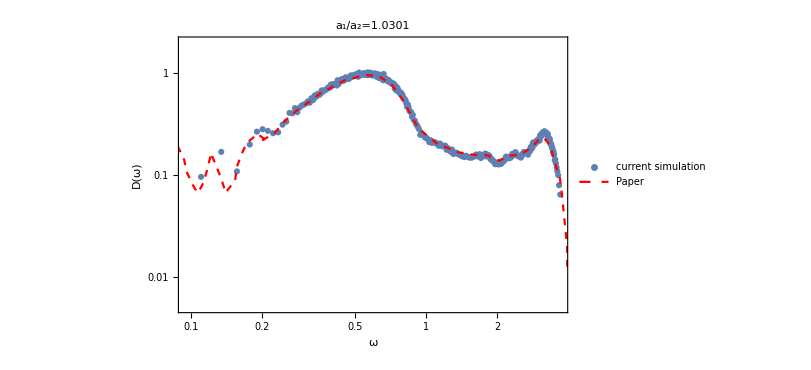

```mathematica
binWidth=300;
Dos=Table[{(omega[[(i+1)*binWidth]]+omega[[i*binWidth]])/2,binWidth/(omega[[(i+1)*binWidth]]-omega[[i*binWidth]])/Length[omega]},{i,Floor[Length[omega]/binWidth]-2}];
plot10301=Show[ListLogLogPlot[Dos,FrameLabel->{"ω","D(ω)"},PlotLegends->{"current simulation"},PlotRange->{All,{0.005,2}}],ListLogLogPlot[omegaPaper,Joined->True,PlotStyle->{Dashed,Red},PlotLegends->{"Paper"}],PlotLabel->"a_1/a_2=1.0301",ImageSize->600]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/bestmatchDomega.jpeg",plot10301,ImageResolution->600]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/bestmatchDomega.jpeg

```mathematica
plist={3.70,3.72,3.74,3.76,3.78,3.80};
```

```mathematica
Pstring=ToString[NumberForm[#,{9,3},ExponentFunction->(Null&)]]&/@plist
```

{3.700,3.720,3.740,3.760,3.780,3.800}

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/inherentgAffineG_Bi_NoNormalization_N512_p"<>Pstring[[6]]<>"_KA1.0000_alpha1.0301.nc","Data"][[1]]
```

Import::format: Cannot import data as Data.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

$Failed⟦1⟧

```mathematica
ka1=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/localTest/inherentg/N512/inherentgAffineG_Bi_NoNormalization_N512_p"<>Pstring[[p]]<>"_KA1.0000_alpha1.0301.nc","Data"][[1]],{p,5}];
```

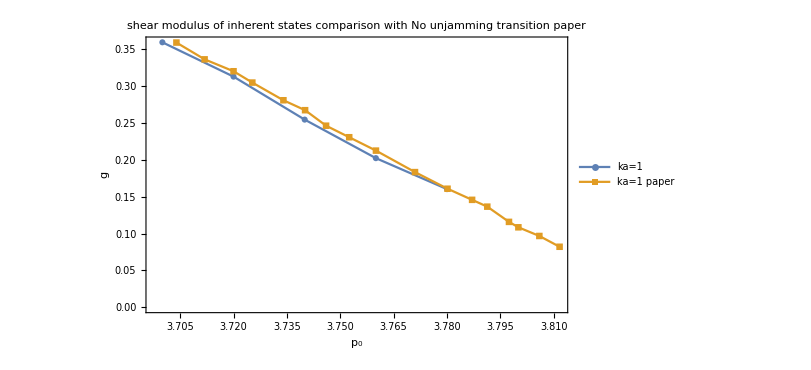

```mathematica
comparisonPlot=ListPlot[{Table[{plist[[p]],Mean[Normal[ka1[[p]]]]},{p,5}],ka1paper},PlotLegends->{"ka=1","ka=1 paper"},PlotMarkers->Automatic,PlotLabel->"shear modulus of inherent states
comparison with No unjamming transition paper",ImageSize->600,PlotRange->All,Joined->True,FrameLabel->{"p_0","g"}]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG2.jpeg",comparisonPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/inherentG2.jpeg

```mathematica
ka001paper={{3.700290275761974,0.35321790036645884},
{3.7100435413642963,0.3254284487528356},
{3.72,0.2998253348649752},
{3.7303628447024675,0.2717463384608707},
{3.7401161103047897,0.2462969732032361},
{3.7472278664731498,0.2306690483206846},
{3.7543396226415098,0.2090666197558951},
{3.7600290275761976,0.19261828373526146},
{3.769375907111756,0.16620365470595697},
{3.780145137880987,0.13878698920837695},{3.7884760522496372,0.11400909592048815},
{3.795791001451379,0.09677543331340013},
{3.8000580551523946,0.08488395818952281}};
```

```mathematica
ka1paper={{3.703947750362845,0.35905430842063735},{3.711872278664732,0.33627175576570095},
{3.72,0.3201386271998944},
{3.7252830188679247,0.30477950903745404},
{3.7340203193033386,0.2808009524285364},
{3.7401161103047897,0.26732911666101833},
{3.7460087082728593,0.2462969732032361},
{3.7525108853410742,0.2306690483206846},
{3.7600290275761976,0.21252113919598364},
{3.77100145137881,0.18337714027808946},
{3.780145137880987,0.16084430702439717},
{3.787053701015965,0.14578104787522406},
{3.791320754716981,0.13653101432481698},
{3.7974165457184323,0.11589292911520903},
{3.8000580551523946,0.1085393430476416},
{3.8059506531204645,0.09677543331340013},
{3.8116400580551524,0.08214681835147608},};
```